# Geonium Theory -- (Brown and Gabrielse)

Notebook is based on paper by Brown and Gabrielse
https : // doi . org/10.1103/RevModPhys .58 .233

```mathematica
ClearAll["Global`*"]
```

### Various assumptions used throughout the notebook

```mathematica
assums={pz>0,ωz>0,m>0,ℏ>0,ℏ∈Reals,Vxp>0,Vyp>0,ωp≥ωm≥0,Vxm>0,Vym>0,n>0,k>0,l>0,ωc>0,ρx∈Reals,ρy∈Reals,ρdotx∈Reals,ρdoty∈Reals,Vzp>0,Vzm>0,z∈Reals,m∈Reals,ωz∈Reals,ωz<ωc/(√2),ωc>√2 ωz,gfunc∈Reals,a∈Reals,√(ωc^2-2 ωz^2)≠0};
$Assumptions=assums;
```

### Eq. 2.14 (Brown Gabrielse) Variable Definitions: ωp=ω_+ ωm=ω_-

```mathematica
ωp=1/2*(ωc+Sqrt[ωc^2-2*ωz^2]);
ωm=1/2*(ωc-Sqrt[ωc^2-2*ωz^2]);
```

```mathematica
FullSimplify[ωp+ωm,assums]
FullSimplify[ωp-ωm,assums]
```

ωc

√(ωc^2-2 ωz^2)

```mathematica
gSubs={√(ωc^2-2 ωz^2)->ωωp-ωωm,ωc^2-2 ωz^2->(ωωp-ωωm)^2};
```

### cyclotron and magnetron components of the motion are separated by introducing two vectors V^(+) and V^(-) Eq. 2.13 (Brown Gabrielse) Variable Definitions: VpVal=V^(+) VmVal=V^(-) ρdotx=(ρ̇)_x ρdoty=(ρ̇)_y

```mathematica
ρVal={ρx,ρy,0};
VpVal={ρdotx,ρdoty,0}-ωm*Cross[{0,0,1},ρVal]
VmVal={ρdotx,ρdoty,0}-ωp*Cross[{0,0,1},ρVal]
```

{ρdotx+1/2 ρy (ωc-√(ωc^2-2 ωz^2)),ρdoty-1/2 ρx (ωc-√(ωc^2-2 ωz^2)),0}

{ρdotx+1/2 ρy (ωc+√(ωc^2-2 ωz^2)),ρdoty-1/2 ρx (ωc+√(ωc^2-2 ωz^2)),0}

### The solution to the radial equation of motion as seen in Eq. 2.18 (Brown Gabrielse) Variable Definitions: ρxVal=ρ_x ρyxVal=ρ_y ρzVal=ρ_z ωp=ω_+ ωm=ω_- V_+={Vxp,Vyp,Vzp} V_-={Vxm,Vym,Vzm}

```mathematica
(*{ρxVal,ρyVal,ρzVal}==FullSimplify[1/(ωp-ωm)(-Cross[{0,0,1},(VpVal-VmVal)]),assums]*)
```

```mathematica
(*{ρxVal,ρyVal,ρzVal}==FullSimplify[1/(ωp-ωm)(-Cross[{0,0,1},({Vxp,Vyp,0}-{Vxm,Vym,0})]),assums]*)
```

## Here we define the raising and lowering operators for the system

### Definitions of the creation and annihilation operators for axial motion Eq. 2.30 (Brown Gabrielse) Variable Definitions: az=a_z azd=a_z^† ωz=ω_z pz=p_z

```mathematica
azOp=(((m*ωz)/(2*ℏ))^(1/2)*z*#+I*(1/(2*m*ℏ*ωz))^(1/2)*(-I*ℏ)D[#,z])&;
azdOp=(((m*ωz)/(2*ℏ))^(1/2)*z*#-I*(1/(2*m*ℏ*ωz))^(1/2)*(-I*ℏ)D[#,z])&;
```

```mathematica
VxpOp=((-(I*ℏ))/m D[#,ρx]-1/2*(Sqrt[ωc^2-2*ωz^2])*ρy*#)&;
VxmOp=((-(I*ℏ))/m D[#,ρx]+1/2*(Sqrt[ωc^2-2*ωz^2])*ρy*#)&;

VypOp=((-(I*ℏ))/m D[#,ρy]+1/2*(Sqrt[ωc^2-2*ωz^2])*ρx*#)&;
VymOp=((-(I*ℏ))/m D[#,ρy]-1/2*(Sqrt[ωc^2-2*ωz^2])*ρx*#)&;
```

### Eq. 2.48 Here we define the raising and lowering operators for the radial motion Variable Definitions: ap=a_+ am=a_- amd=(a_-)^† apd=(a_+)^†

```mathematica
coeff=(m/(2*ℏ(ωp-ωm)))^(1/2);
apOp=FullSimplify[coeff*(VxpOp[#]-I*VypOp[#])]&;
amOp=FullSimplify[coeff*(VxmOp[#]+I*VymOp[#])]&;
apdOp=FullSimplify[coeff*(VxpOp[#]+I*VypOp[#])]&;
amdOp=FullSimplify[coeff*(VxmOp[#]-I*VymOp[#])]&;
```

### Normalization of the full ground state wave function

```mathematica
FullSimplify[Solve[azOp[Exp[-ao*z^2]]==0,ao]//Quiet,assums]
```

{{ao→(m ωz)/(2 ℏ)}}

```mathematica
ψo1T=Exp[aa*(ρx^2+ρy^2)]*Exp[-m/(2*ℏ)*ωz *z^2]
Solve[FullSimplify[apOp[ψo1T]==0,assums],aa]//Quiet
Solve[FullSimplify[amOp[ψo1T]==0,assums],aa]//Quiet
```

ⅇ^(aa (ρx^2+ρy^2)-(m z^2 ωz)/(2 ℏ))

{{aa→-(m √(ωc^2-2 ωz^2))/(4 ℏ)}}

{{aa→-(m √(ωc^2-2 ωz^2))/(4 ℏ)}}

```mathematica
ψo1=FullSimplify[Exp[-m/(4*ℏ) *(ωp-ωm)*(ρx^2+ρy^2)]*Exp[-m/(2*ℏ)*ωz *z^2],assums]
```

ⅇ^(-(m (2 z^2 ωz+(ρx^2+ρy^2) √(ωc^2-2 ωz^2)))/(4 ℏ))

#### <n, l, k |n, l, k> = a^2

```mathematica
norm1=Values[Flatten[FullSimplify[
Solve[Assuming[assums,a^2*Integrate[
Conjugate[ψo1]*ψo1,
{ρx,-∞,∞},
{ρy,-∞,∞},
{z,0,∞},
GenerateConditions->False]]==1,a],
assums]]][[-1]]
```

(((m^3 ωz (ωc^2-2 ωz^2))/ℏ^3)^(1/4))/π^(3/4)

#### The Normalized ground state wave function

```mathematica
ψo=FullSimplify[ψo1*norm1,assums]
```

(ⅇ^(-(m (2 z^2 ωz+(ρx^2+ρy^2) √(ωc^2-2 ωz^2)))/(4 ℏ)) ((m^3 ωz (ωc^2-2 ωz^2))/ℏ^3)^(1/4))/π^(3/4)

```mathematica
FullSimplify[ψo/.gSubs,assums]
```

(ⅇ^(-(m (2 z^2 ωz+(ρx^2+ρy^2) (-ωωm+ωωp)))/(4 ℏ)) ((m^3 ωz (ωωm-ωωp)^2)/ℏ^3)^(1/4))/π^(3/4)

#### Check that the wavefunction is in fact normalized <n, l, k |n, l, k> = 1

```mathematica
FullSimplify[
Assuming[assums,
Integrate[Conjugate[ψo]*ψo,
{ρx,-∞,∞},
{ρy,-∞,∞},
{z,0,∞}]]==1,
assums]
```

True

#### a_z |n, l, k> = 0

```mathematica
FullSimplify[azOp[ψo],assums]==0
```

True

#### a_± |0,0,0>= 0 ???

```mathematica
FullSimplify[apOp[ψo],assums]==0
FullSimplify[amOp[ψo],assums]==0
```

True

True

#### Full wave function defined using raising and lowering functions acting on the ground state.

```mathematica
Clear[ψFull]
ψFull[n_,l_,k_]:=
ψFull[n,l,k]=
FullSimplify[
1/Sqrt[n!]*Nest[apdOp,
1/Sqrt[l!]*Nest[amdOp,
1/Sqrt[k!]*Nest[azdOp,
ψo,k],l],n],assums]
```

```mathematica
Clear[ψs]
ψs[s_,n_,l_,k_]:=
ψs[s,n,l,k]=
If[s==1,
ψFull[n,l,k]*{1,0},
If[s==-1,
ψFull[n,l,k]*{0,1},0,0],
0]
```

## Here we create the H_z Hamiltonian See: Eq. 2.33

```mathematica
Hz=ℏ*ωz*(azdOp[azOp[#]]+1/2#)&;
```

#### Function returns the eigenvalue H_z ψ=Eψ

```mathematica
Enz[n_,l_,k_]:=Flatten@FullSimplify[Solve[Hz[ψFull[n,l,k]]==a*ψFull[n,l,k],a]//Quiet,assums]
```

#### System should behave as a harmonic oscillator in the z direction H_z ψ=Eψ E_n=(2n+1)

```mathematica
ParallelTable[Values[Enz[in,il,ik]][[1]]==(2ik+1)(ℏ*ωz)/2,
{ik,0,4},
{in,0,2},
{il,0,2}]
```

{{{True,True,True},{True,True,True},{True,True,True}},{{True,True,True},{True,True,True},{True,True,True}},{{True,True,True},{True,True,True},{True,True,True}},{{True,True,True},{True,True,True},{True,True,True}},{{True,True,True},{True,True,True},{True,True,True}}}

## Here we create the H_ρ Hamiltonian See: Eq. 2.50

```mathematica
Hρ=(ℏ*ωp*(apdOp[apOp[#]]+1/2#)-ℏ*ωm*(amdOp[amOp[#]]+1/2#))&;
```

#### Test if Function returns the eigenvalue H_ρ ψ=Eψ E_n=(ℏ*ωp*(n+1/2)-ℏ*ωm*(l+1/2))

```mathematica
Enρ[n_,l_,k_]:=Flatten@FullSimplify[Solve[Hρ[ψFull[n,l,k]]==a*ψFull[n,l,k],a]//Quiet,assums]
```

```mathematica
ParallelTable[FullSimplify[Values[Enρ[in,il,ik]][[1]]==(ℏ*ωp*(in+1/2)-ℏ*ωm*(il+1/2)),assums],
{ik,0,2},
{in,0,2},
{il,0,2}]
```

{{{True,True,True},{True,True,True},{True,True,True}},{{True,True,True},{True,True,True},{True,True,True}},{{True,True,True},{True,True,True},{True,True,True}}}

## Here we create the H_s Hamiltonian See: Eq. 2.61

```mathematica
Hs=(gfunc/2*ℏ*ωc*1/2*PauliMatrix[3].#)&;
```

```mathematica
Ens[s_,n_,l_,k_]:=Flatten@FullSimplify[Solve[Hs[ψs[s,n,l,k]]==a*ψs[s,n,l,k],a]//Quiet,assums]
```

#### Test if Function returns the eigenvalue H_s ψ= E_s ψ E_n=gfunc/2 ℏω_c s/2

```mathematica
ParallelTable[Values[Ens[is,in,il,ik]][[1]]==
gfunc/2*ℏ*ωc*is/2,
{is,-1,1,2},
{ik,0,2},
{in,0,2},
{il,0,2}]
```

{{{{True,True,True},{True,True,True},{True,True,True}},{{True,True,True},{True,True,True},{True,True,True}},{{True,True,True},{True,True,True},{True,True,True}}},{{{True,True,True},{True,True,True},{True,True,True}},{{True,True,True},{True,True,True},{True,True,True}},{{True,True,True},{True,True,True},{True,True,True}}}}

## Here we create the full Hamiltonian See: Eq. 2.50

```mathematica
ham=(Hs[#]+Hρ[#]+Hz[#])&;
```

```mathematica
En[s_,n_,l_,k_]:=Flatten@FullSimplify[Solve[ham[ψs[s,n,l,k]]==a*ψs[s,n,l,k],a]//Quiet,assums]
```

#### Test if Function returns the eigenvalue H_s ψ= E ψ E_n=(g/2 ℏω_c s/2+(2k+1)(ℏω_z)/2+ℏω_p*(n+1/2)-ℏω_m(l+1/2))

```mathematica
ParallelTable[FullSimplify[Values[En[is,in,il,ik]][[1]]==(gfunc/2*ℏ*ωc*is/2+(2*ik+1)(ℏ*ωz)/2+ℏ*ωp*(in+1/2)-ℏ*ωm*(il+1/2)),assums],
{is,-1,1,2},
{ik,0,2},
{in,0,2},
{il,0,2}]
```

{{{{True,True,True},{True,True,True},{True,True,True}},{{True,True,True},{True,True,True},{True,True,True}},{{True,True,True},{True,True,True},{True,True,True}}},{{{True,True,True},{True,True,True},{True,True,True}},{{True,True,True},{True,True,True},{True,True,True}},{{True,True,True},{True,True,True},{True,True,True}}}}

#### The different spin states are orthogonal

```mathematica
{Conjugate[ψs[1,0,0,0]].ψs[-1,0,0,0],
Conjugate[ψs[1,0,0,0]].ψs[-1,1,0,0],
Conjugate[ψs[1,0,0,0]].ψs[-1,2,0,0]}
```

{0,0,0}

#### the wave function is properly normalized

```mathematica
{FullSimplify[Assuming[assums,Integrate[Conjugate[ψs[1,0,0,0]].ψs[1,0,0,0],
{ρx,-∞,∞},
{ρy,-∞,∞},
{z,0,∞}]],assums],
FullSimplify[Assuming[assums,Integrate[Conjugate[ψs[-1,0,0,0]].ψs[-1,0,0,0],
{ρx,-∞,∞},
{ρy,-∞,∞},
{z,0,∞}]],assums]}
```

{1,1}

#### cyclotron states are orthogonal

```mathematica
FullSimplify[Assuming[assums,Integrate[Conjugate[ψs[1,1,0,0]].ψs[1,0,0,0],
{ρx,-∞,∞},
{ρy,-∞,∞},
{z,0,∞}]],assums]
```

0

#### magneton states are orthogonal

```mathematica
FullSimplify[Assuming[assums,Integrate[Conjugate[ψs[1,0,1,0]].ψs[1,0,1,0],
{ρx,-∞,∞},
{ρy,-∞,∞},
{z,0,∞}]],assums]
FullSimplify[Assuming[assums,Integrate[Conjugate[ψs[1,0,1,0]].ψs[1,0,0,0],
{ρx,-∞,∞},
{ρy,-∞,∞},
{z,0,∞}]],assums]
```

1

0

```mathematica
FullSimplify[Assuming[assums,Integrate[Conjugate[ψs[1,0,1,1]].ψs[1,0,0,1],
{ρx,-∞,∞},
{ρy,-∞,∞},
{z,0,∞}]],assums]
```

0

```mathematica
FullSimplify[Assuming[assums,Integrate[Conjugate[ψs[1,0,1,0]].ψs[1,0,0,1],
{ρx,-∞,∞},
{ρy,-∞,∞},
{z,0,∞}]],assums]
```

0

```mathematica
FullSimplify[Assuming[assums,Integrate[Conjugate[ψs[1,0,0,0]].ψs[1,0,0,1],
{ρx,-∞,∞},
{ρy,-∞,∞},
{z,0,∞}]],assums]
```

√(2/π)

```mathematica
{FullSimplify[Assuming[assums,Integrate[Conjugate[ψs[1,0,0,0]].ψs[1,0,0,1],
{ρx,-∞,∞},
{ρy,-∞,∞},
{z,0,∞}]],assums],
FullSimplify[Assuming[assums,Integrate[Conjugate[ψs[1,0,0,1]].ψs[1,0,0,2],
{ρx,-∞,∞},
{ρy,-∞,∞},
{z,0,∞}]],assums],
FullSimplify[Assuming[assums,Integrate[Conjugate[ψs[1,0,0,2]].ψs[1,0,0,3],
{ρx,-∞,∞},
{ρy,-∞,∞},
{z,0,∞}]],assums],
FullSimplify[Assuming[assums,Integrate[Conjugate[ψs[1,0,0,3]].ψs[1,0,0,4],
{ρx,-∞,∞},
{ρy,-∞,∞},
{z,0,∞}]],assums],
FullSimplify[Assuming[assums,Integrate[Conjugate[ψs[1,0,0,4]].ψs[1,0,0,5],
{ρx,-∞,∞},
{ρy,-∞,∞},
{z,0,∞}]],assums]}
```

{√(2/π),1/(√π),√(3/(2 π)),3/(2 √(2 π)),3/4 √(5/(2 π))}

```mathematica
{FullSimplify[Assuming[assums,Integrate[Conjugate[ψs[1,0,0,1]].ψs[1,0,0,0],
{ρx,-∞,∞},
{ρy,-∞,∞},
{z,0,∞}]],assums],
FullSimplify[Assuming[assums,Integrate[Conjugate[ψs[1,0,0,0]].ψs[1,0,0,1],
{ρx,-∞,∞},
{ρy,-∞,∞},
{z,0,∞}]],assums],
FullSimplify[Assuming[assums,Integrate[Conjugate[ψs[1,0,0,1]].ψs[1,0,0,2],
{ρx,-∞,∞},
{ρy,-∞,∞},
{z,0,∞}]],assums],
FullSimplify[Assuming[assums,Integrate[Conjugate[ψs[1,0,0,2]].ψs[1,0,0,1],
{ρx,-∞,∞},
{ρy,-∞,∞},
{z,0,∞}]],assums]}
```

{√(2/π),√(2/π),1/(√π),1/(√π)}

```mathematica
ParallelTable[
FullSimplify[Assuming[assums,
Integrate[
Conjugate[ψs[1,0,0,i]].ψs[1,0,0,i+1],
{ρx,-∞,∞},
{ρy,-∞,∞},
{z,0,∞}]],assums],
{i,0,5}]
```

{√(2/π),1/(√π),√(3/(2 π)),3/(2 √(2 π))}

```mathematica
ParallelTable[
FullSimplify[Assuming[assums,
Integrate[
Conjugate[ψs[1,0,1,i]].ψs[1,0,1,i+1],
{ρx,-∞,∞},
{ρy,-∞,∞},
{z,0,∞}]],assums],
{i,0,3}]
```

{√(2/π),1/(√π),√(3/(2 π)),3/(2 √(2 π))}

```mathematica
ParallelTable[
Assuming[assums,
Integrate[
Conjugate[ψs[1,0,1,0]].ψs[1,0,1,i],
{ρx,-∞,∞},
{ρy,-∞,∞},
{z,0,∞},
GenerateConditions->False]],
{i,0,7}]
```

```mathematica
Assuming[assums,
Integrate[Conjugate[ψs[1,1,0,0]].ψs[1,1,0,1],
{ρx,-∞,∞},
{ρy,-∞,∞},
{z,0,∞}]]
```

√(2/π)

```mathematica
{Assuming[assums,
Integrate[Conjugate[ψs[1,1,0,0]].ψs[1,1,0,2],
{ρx,-∞,∞},
{ρy,-∞,∞},
{z,0,∞}]],
Assuming[assums,
Integrate[Conjugate[ψs[1,1,0,0]].ψs[1,1,0,3],
{ρx,-∞,∞},
{ρy,-∞,∞},
{z,0,∞}]]}
```

{0,-1/(√(3 π))}

```mathematica
Assuming[assums,
Integrate[Conjugate[ψs[1,0,0,0]].ψs[1,0,0,3],
{ρx,-∞,∞},
{ρy,-∞,∞},
{z,0,∞}]]
```

-1/(√(3 π))

```mathematica
diagTerms[ik1_,ik2_]:=
FullSimplify[
Assuming[assums,
Integrate[Conjugate[ψs[1,0,0,ik1]].Evaluate[FullSimplify[ham[ψs[1,0,0,ik2]]]],
{ρx,-∞,∞},
{ρy,-∞,∞},
{z,0,∞}]]/Values[En[1,0,0,ik2]][[1]],assums]
```

```mathematica
diagTerms[0,5]
```

1/2 √(3/(5 π))

## Here we test that all of the commutation relations outlined in Brown Gabrielse hold for our operators See: Eq. 2.31 and Eq. 2.49

```mathematica
(* A function to return the value of the commutator of two operators *)
comRels[o1_,o2_]:=
Values[Flatten@Solve[FullSimplify[o1[o2[ϕ[x,y,z]]]-o2[o1[ϕ[x,y,z]]]==com*ϕ[x,y,z],assums],com]//Quiet][[1]]
```

#### The commutation relations for the axial operators [a_z,a_z^†]=1 Eq. 2.31 Variable Definitions: az=a_z azd=a_z^†

```mathematica
comRels[azOp,azdOp]==1
```

True

#### Here we show that all commutations of the axial raising and lowering operators except for [a_z,a_z^†]=1 go to zero Eq. 2.49 Variable Definitions: az=a_z azd=a_z^†

```mathematica
{comRels[azOp,azOp]==0,
comRels[azdOp,azdOp]==0}
```

{True,True}

#### The commutation relations for the radial operators [a_±,(a_±)^†]=1 Eq. 2.49 Variable Definitions: ap=a_+ am=a_- amd=(a_-)^† apd=(a_+)^†

```mathematica
{comRels[apOp,apdOp]==1,
comRels[amOp,amdOp]==1}
```

{True,True}

#### Here we show that all commutations of the radial raising and lowering operators except for [a_±,(a_±)^†]=1 go to zero Eq. 2.49 Variable Definitions: ap=a_+ am=a_- amd=(a_-)^† apd=(a_+)^†

```mathematica
{comRels[apOp,apOp]==0,
comRels[apOp,amOp]==0,
comRels[apOp,amdOp]==0,
comRels[amOp,amOp]==0,
comRels[amOp,apOp]==0,
comRels[amOp,apdOp]==0}
```

{True,True,True,True,True,True}

### Here we check the action of the raising and lowering operators acting on the full wavefunction

#### (a_+)^† |n, l, k> = Sqrt[ n+1 ] |n+1, l, k> (a_-)^† |n, l, k> = Sqrt[ q+1 ] |n, l+1, k> a_z^† |n, l, k> = Sqrt[ k+1 ] |n, l, k+1>

```mathematica
{ParallelTable[
FullSimplify[
apdOp[ψFull[inf,0,0]]==Sqrt[inf+1]*ψFull[inf+1,0,0],assums],
{inf,0,9}],
ParallelTable[
FullSimplify[
amdOp[ψFull[0,il,0]]==Sqrt[il+1]*ψFull[0,il+1,0],assums],
{il,0,9}],
ParallelTable[
FullSimplify[
azdOp[ψFull[0,0,ik]]==Sqrt[ik+1]*ψFull[0,0,ik+1],assums],
{ik,0,9}]}
```

{{True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True},{True,True,True,True,True,True,True,True,True,True}}

#### Here we test the raising and lowering operators for higher excitation values. (a_+)^† |n, q, k> = Sqrt[ n+1 ] |n+1, q, k> (a_-)^† |n, q, k> = Sqrt[ q+1 ] |n, q+1, k> a_z^† |n, q, k> = Sqrt[ k+1 ] |n, q, k+1>

```mathematica
(* This function is used to take the limit ωz<<ωc for any
inequality that returnes niether true nor false to see if taking the
limit returns true *)
seriesTest[f_]:=
ParallelTable[If[f[[i]][[j]][[k]],
f[[i]][[j]][[k]],
False,
FullSimplify[
Normal@Series[f[[i]][[j]][[k]],{ωz,0,2}],
assums]],
{i,Length[f]},
{j,Length[f[[i]]]},
{k,Length[f[[i]][[j]]]}]
```

```mathematica
{ParallelTable[
FullSimplify[
apdOp[ψFull[in,0,ik]]==Sqrt[in+1]*ψFull[in+1,0,ik],assums],
{in,0,3},
{ik,0,3}],
ParallelTable[
FullSimplify[
amdOp[ψFull[0,il,ik]]==Sqrt[il+1]*ψFull[0,il+1,ik],assums],
{il,0,3},
{ik,0,3}],
ParallelTable[
FullSimplify[
azdOp[ψFull[in,il,ik]]==Sqrt[ik+1]*ψFull[in,il,ik+1],assums],
{in,0,2},
{il,0,2},
{ik,0,3}]}
```

{{{True,True,True,True},{True,True,True,True},{True,True,True,True},{True,True,True,True}},{{True,True,True,True},{True,True,True,True},{True,True,True,True},{True,True,True,True}},{{{True,True,True,True},{True,True,True,True},{True,True,True,True}},{{True,True,True,True},{True,True,True,True},{True,True,True,True}},{{True,True,True,True},{True,True,True,True},{True,True,True,True}}}}

#### Numerical values given in the paper

```mathematica
fNumbs={
gfunc->5.59,
ℏ->1,
m->0.5*10^6,
ωc->6.0*10^-4,
ωz->2.6*10^-7,
αc->3.4*10^-5};
```

#### Here we start by evaluating the ψ^*ψ and creating 2d Plots

```mathematica
Clear[NPlot]
NPlot[s_,n_,l_,k_,ix_,iy_,iz_]:=
NPlot[s,n,l,k,ix,iy,iz]=Re@(Conjugate[ψs[s,n,l,k]].ψs[s,n,l,k])/.fNumbs/.{ρx->ix,ρy->iy,z->iz}
```

```mathematica
zZeroDat2=Flatten[
ParallelTable[{ix,iy,NPlot[-1,3,0,2,ix,iy,0]//Quiet},{ix,-.25,.25,.001},
{iy,-.25,.25,.001}],1];
yZeroDat2=Flatten[
ParallelTable[{ix,iz,NPlot[-1,3,0,2,ix,0,iz]//Quiet},{ix,-.25,.25,.001},
{iz,-8,8,.2}],1];
```

```mathematica
GraphicsRow[{
ListDensityPlot[zZeroDat2],
ListDensityPlot[yZeroDat2]},
ImageSize->500]
```

-Graphics-

```mathematica
plotWaveFunctionP[s_,n_,l_,k_, rot_] := (
    (* Here we write the wave functions for the penning trap:
    n:    (int) cyclotron quantum number 
    k:    (int) axial quantum number
    l:    (int) magnaton quantum number 
    rot:  (float) an angle controlling the viewpoint of
           the camera about the z-axis rot=0 returns a view
           of the x-y plane *)

  (* this controls the scale of the area being to be plotted
  currently region function is set to be a sphere about the origin
  with a radius .9*zScale *)
zScale=1;
xScale=zScale;
yScale=zScale;
perf="Quality";

(* Numbers given in paper *)
fNumbs={
gfunc->2,
ℏ->1,
m->0.5*10^6,
ωc->6.0*10^-4,
ωz->2.6*10^-7,
αc->3.4*10^-5};

(* Square of the wave function *)
NPlot2[ix_,iy_,iz_]:=
Re@(Conjugate[ψs[s,n,l,k]].ψs[s,n,l,k])/.fNumbs/.{ρx->ix,ρy->iy,z->iz};

(* Create the numerical data for the plot *)
data3d=
Flatten[
ParallelTable[
{ix,iy,iz,NPlot2[ix,iy,iz]//Quiet},
{ix,-.25,.25,.005},
{iy,-.25,.25,.005},
{iz,-8,8,.4}],
2];

Legended[
ListDensityPlot3D[
data3d,
ColorFunction->"SunsetColors",
ColorFunctionScaling -> True,
ViewVector -> {2*xScale*Cos[rot], 2*yScale*Sin[rot],30},
PerformanceGoal->perf,
BoxRatios->{xScale, yScale, zScale},
PlotTheme->"Scientific",
Background->White,
Boxed->False,
Axes-> False,
ImageSize -> 500,
ImagePadding -> None,
RegionFunction ->
Function[{x, y, z, f}, x^2 + y^2 + z^2 <= (10.25*zScale)^2]],
Placed[
 Framed[
 Style[
"s="<>ToString[s]<>"  n=" <> ToString[n] <> "  l=" <> ToString[l] <> "  k=" <>  ToString[k],
Black,
25,
FontFamily -> "Latex",
DigitBlock -> 3],
FrameStyle -> Black,
RoundingRadius -> 10,
FrameMargins -> 2,
Background -> CMYKColor[0, 0, 0, 0, .7]],
{.5, .125}]])
```

```mathematica
Row[{
plotWaveFunctionP[1,3,0,0,π/4],
plotWaveFunctionP[1,3,0,2,π/4]},
Background->White]
```

-Graphics--Graphics-

```mathematica
plFun[s_,n_,l_,k_]:=Export[FileNameJoin[{NotebookDirectory[],"data","figs","s"<>ToString[s]<>"_n"<>ToString[n]<>"_l"<>ToString[l]<>"_k"<>ToString[k]<>".png"}],plotWaveFunctionP[s,n,l,k,π/4]];
```

```mathematica
plFun[1,3,0,1];
```

```mathematica
plFun[1,3,0,2];
plFun[1,3,0,0];
```

```mathematica
nEnLvls[n_]:=(ℏ*ωp*(n+1/2))/.fNumbs
nsEnLvls[s_,n_]:=(gfunc/2*ℏ*ωc*s/2+ℏ*ωp*(n+1/2))/.fNumbs
nszEnLvls[s_,n_,k_]:=(gfunc/2*ℏ*ωc*s/2+ℏ*ωp*(n+1/2)+(2*k+1)((ℏ*ωz)*250)/2)/.fNumbs
EnLvls[s_,n_,l_,k_]:=(gfunc/2*ℏ*ωc*s/2+(2*k+1)((ℏ*ωz)*250)/2+ℏ*ωp*(n+1/2)-ℏ*ωm*(l+1/2)*10^6)/.fNumbs
```

```mathematica
nVals=Table[
Table[{x,nEnLvls[n]},{x,0,.8,1/20}],
{n,0,3}];

nsuVals=Table[
Table[{x,nsEnLvls[1,n]},{x,1.2,1.8,1/20}],
{n,0,3}];
nsdVals=Table[
Table[{x,nsEnLvls[-1,n]},{x,1.2,1.8,1/20}],
{n,0,3}];
```

```mathematica
nsdzVals=Table[
Table[{x,nszEnLvls[-1,0,ik]},{x,2.2,2.8,1/20}],
{ik,0,4}];
```

```mathematica
nsdzlVals=Table[
Table[{x,EnLvls[-1,0,il,0]},{x,3.2,3.8,1/20}],
{il,0,4}];
```

```mathematica
cols={Red,Blue,Black,Purple};
cols2={Red,Darker[Red],Darker[Red],Darker[Red],Darker[Red]};
```

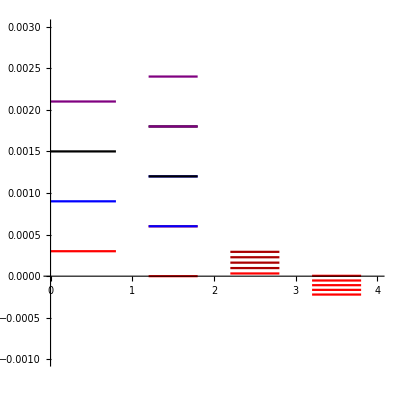

```mathematica
(* note energy levels for axial binding and magnetron motion are not drawn to scale, in order to better show seperation *)
(* need to come back and connect matching colored lines *)
Show[{
ListLinePlot[nVals,
PlotRange->{{0,4},{-.001,.003}},
Axes->{False,True},
AspectRatio->1,
PlotStyle->cols],
ListLinePlot[nsuVals,
PlotStyle->cols],
ListLinePlot[nsdVals,
PlotStyle->cols],
ListLinePlot[nsdzVals,
PlotStyle->cols2],
ListLinePlot[nsdzlVals,
PlotStyle->Red]}]
```